# Examen 020712

## Current function

```mathematica
DSolve[{D[ψ[x,y],y]==-x/(2*Sqrt[y]),D[ψ[x,y],x]==-Sqrt[y]},ψ[x,y],{x,y}]
```

{{ψ[x,y]→-x √y+C[1]}}

## Potential and vorticity

```mathematica
DSolve[{D[ϕ[x,y],x]==-x/(2*Sqrt[y]),D[ϕ[x,y],y]==Sqrt[y]},ϕ[x,y],{x,y}]
```

DSolve[{ϕ^(1,0)[x,y]==-x/(2 √y),ϕ^(0,1)[x,y]==√y},ϕ[x,y],{x,y}]

```mathematica
Curl[{-x/(2*Sqrt[y]),Sqrt[y]},{x,y}](*It's rotational .af\_(ツ)_/.af*)
```

-x/(4 y^(3/2))

## Streamline/vector field

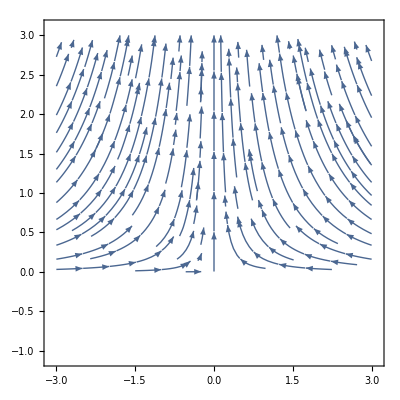

```mathematica
StreamPlot[{-x/(2*Sqrt[y]),Sqrt[y]},{x,-3,3},{y,-1,3}]
```